```mathematica
ClearAll["Global`*"]
```

```mathematica
Data=Import["D:\\sebas\\estudios\\exactas\\materias\\materiasdf\\incertezas\\doble_exp.dat","Table","HeaderLines"->1];x=Data[[All,1]];y=Data[[All,2]];
```

```mathematica
DataPlot=ListLogPlot[Data,PlotMarkers->{Automatic, 10}];
```

```mathematica
f[x_,a_,b_,c_,d_,e_]:=a+b*Exp[-x/d]+c*Exp[-x/e]
```

```mathematica
S[a_,b_,c_,d_,e_]:=Sum[((y[[i]]-f[x[[i]],a,b,c,d,e])/y[[i]])^2,{i,1,Length[y]}]
```

```mathematica
res =FindMinimum[S[a,b,c,d,e],{{a,10},{b,130},{c,1000},{d,200},{e,35}}];
```

```mathematica
res[[2]]
```

{a→8.06945,b→108.561,c→886.315,d→238.327,e→38.3593}

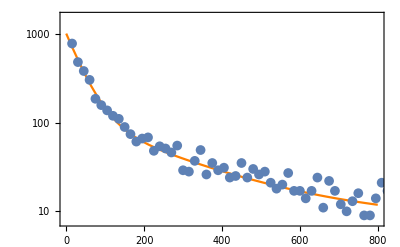

```mathematica
Show[{LogPlot[f[x,a,b,c,d,e]/.res[[2]],{x,0,800},PlotStyle->Directive[Orange],Frame->True,GridLines->Automatic],DataPlot}]
```

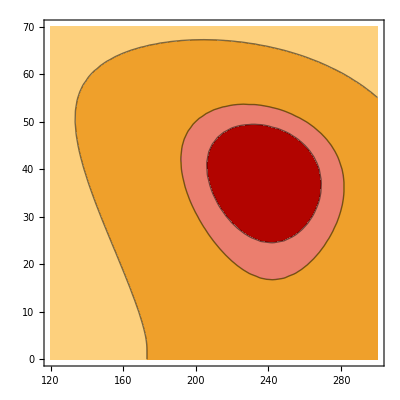

```mathematica
ContourPlot[(S[a,b,c,X,Y]-res[[1]])/.res[[2]],{X,120,300},{Y,0,70},Contours->{1,2,8},ContourShading->ColorData[10,"ColorList"]]
```

```mathematica
ColorData["TemperatureMap","ColorList"]
```

Missing[NotApplicable]

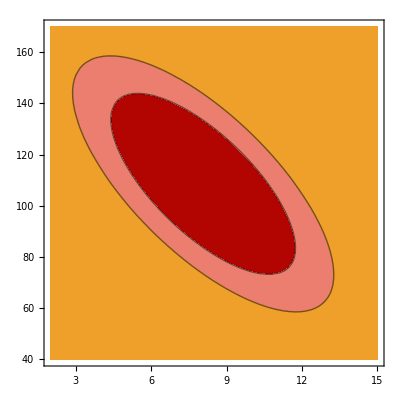

```mathematica
ContourPlot[(S[X,Y,c,d,e]-res[[1]])/.res[[2]],{X,2,15},{Y,40,170},Contours->{1,2},ContourShading->ColorData[10,"ColorList"]]
```